```mathematica
If[StringTake[$SystemID,3]=="Win",
SetDirectory["C:\\Users\\pwrzo\\Documents\\GitHub\\AvoidedQP\\implementation\\"],
SetDirectory["~/Documents/GitHub/AvoidedQP/reimplementation/"]
]
```

/Users/pwrzosek/Documents/GitHub/AvoidedQP/reimplementation

```mathematica
AppendTo[$Path,"~/MathematicaPkg/"];
<<CustomTicks`;
```

```mathematica
getAssoc[head_,JRange_,tail_]:=(
result={};
Do[(
file=StringJoin[head,"_1.0_",J,"_",tail,".json"];
sData=Import[StringJoin["data/", file],"RawJSON"];
result=Join[result,sData];
),{J,JRange}];
result
)
```

```mathematica
getStruct[ds_]:=(
sizeAvail=Normal[DeleteDuplicates[ds[Take,"size"]]];
interactionAvail=Normal[DeleteDuplicates[ds[Take,"interaction"]]];
couplingAvail=Normal[DeleteDuplicates[ds[Take,"coupling"]]];
hoppingAvail=Normal[DeleteDuplicates[ds[Take,"hopping"]]];
<|"size"->sizeAvail,"interaction"->interactionAvail,"coupling" ->couplingAvail, "hopping"->hoppingAvail|>
)
```

```mathematica
extractData[ds_,directive_,keys_,n_]:=(
data=Apply[ds,directive];
{x,y}=Table[(data[Take,keys[[i]]]//Normal)[[1]],{i,1,2}];

Return[Table[{x[[i]],y[[i]]},{i,Length[x]}]]
)
```

```mathematica
getDPlot[spc_,n_]:=(
SetOptions[LinTicks,TickLengthScale->1.5];

plt=ListPlot[spc,
ImageSize->Medium,
Joined->False,
PlotMarkers->{"●",10},
(*Mesh->15,*)
PlotStyle->If[B==0, Purple,Orange](*{Opacity[0.5,Blue]}*),
Frame->True,Axes->False,
FrameStyle->Directive[Black,14,FontFamily->"Bookman Old Style"],
LabelStyle->Directive[Black,14],
(*InterpolationOrder->0,*)
PlotRange->{{-n+1,n-1},{10^-6,1}},
PlotRangeClipping->True,
(*PlotLegends->Placed[Automatic,Right],*)
ClippingStyle->Automatic,
AspectRatio->0.75,
FrameLabel->{"n"," "},Epilog->{
Text[
Style["λ = "<>ToString[NumberForm[B,{2,1}]],Black,24,FontFamily->"Bookman Old Style"],
{3n/5,-2}]
},
ScalingFunctions->"Log",
FrameTicks->{{Table[{10^-l,l},{l,-10,20,1}],Table[{10^-l,""},{l,-10,20,1}]},Automatic}
(*{LinTicks[-n+1,n+1,1,0],LogTicks[10,-5, 0],LinTicks[-n+1,n+1,1,0,ShowTickLabels->False],LogTicks[10,-5,0,ShowTickLabels->False]}*)
];

plt
)
```

```mathematica
makePlotsSpc[]:=(
dirc={Select[#coupling==J&&#size==n&&#interaction==B&]};
keys={"magnons","coefficients"};

plots={};
Do[(
Do[(
buff={};
Do[(
spc=extractData[spcDataset,dirc,keys,n];
AppendTo[buff,getDPlot[spc,n]];
),{B,spcAvail["interaction"]//Normal}];
AppendTo[plots,buff];
),{n,spcAvail["size"]//Normal}];
),{J,spcAvail["coupling"]//Normal}];

plots
)
```

```mathematica
JRange={"0.4"};
tails={"20-2-20_0.0-1.0-1.0"};
head = "mc";
spcPlots={};
Do[(
spcDataset=Dataset[getAssoc[head,JRange,tail]];
spcAvail=Dataset[getStruct[spcDataset]];
AppendTo[spcPlots,makePlotsSpc[]];
),{tail,tails}]
```

```mathematica
spcAvail
```

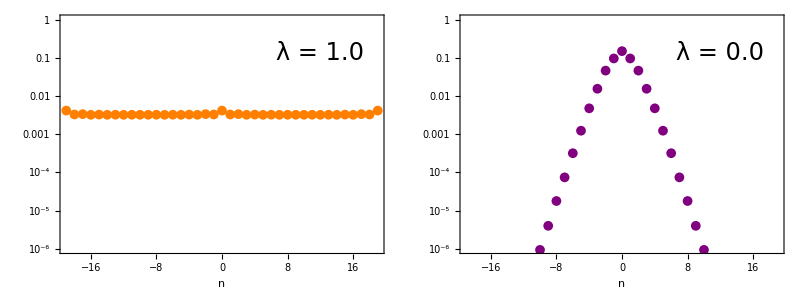

```mathematica
Grid[Reverse[spcPlots[[1]],2]]
```

```mathematica
SavePlots[]:=(
Do[(
Do[(
Do[(
fileName=StringJoin["plots/",head,"/",
head,"_L=",ToString[spcAvail["size"][[iN]]],
"_J=",ToString[spcAvail["coupling"][[iJ]]],
"_B=",ToString[spcAvail["interaction"][[iB]]],
".jpg"];
Export[fileName,spcPlots[[iN,iJ,iB]],ImageResolution->300];
),{iB,Length[spcAvail["interaction"]//Normal]}]
),{iJ,Length[spcAvail["coupling"]//Normal]}]
),{iN,Length[spcAvail["size"]//Normal]}]
)
```

```mathematica
SavePlots[]
```